# L-systems with Turtle Interpretation

## References

Prusinkiewicz P., Lindenmayer A., The Algorithmic Beauty of Plants, Springer-Verlag, NewYork, 1990.

## Definitions

```mathematica
Needs["Turtle`"];
```

### L-system directives

```mathematica
ClearAll[StringToDirective];
Options[StringToDirective]={
"RulesForHeads"->{
"F"->"Forward",
"f"->"forward",
"+"->"Left",
"-"->"Right"
}
};
StringToDirective[string_String,OptionsPattern[]]:=Module[
{
dirList=StringCases[
string,
RegularExpression["([A-Za-z\\+\\-\\[\\]{}])(\\(([^\\)]+)\\))?"]:>{"$1",StringSplit["$3",","]}
],
outputStack={{}},
top
},
Do[
Switch[dir⟦1⟧,
"[",
	AppendTo[outputStack,{}];(* Push *),
"]",
	{{top},outputStack}=TakeDrop[outputStack,-1];(* Pop *)
	AppendTo[outputStack⟦-1⟧,top];,
"F"|"f"|"+"|"-",
	AppendTo[
	outputStack⟦-1⟧,
	(Replace[dir⟦1⟧,OptionValue["RulesForHeads"]])@@ToExpression[dir⟦2⟧]
	];,
_String,
	AppendTo[outputStack⟦-1⟧,dir⟦1⟧@@ToExpression[dir⟦2⟧]];
],
{dir,dirList}
];
Return[First[outputStack]];
]
```

## Applications

### 1

#### Example 1.1: Koch island

```mathematica
ω=StringToDirective["F-F-F-F"];
rule={
"Forward"[]->Sequence@@StringToDirective["F-F+F+FF-F-F+F"]
};
```

```mathematica
dir=Nest[ReplaceAll[rule],ω,3];
```

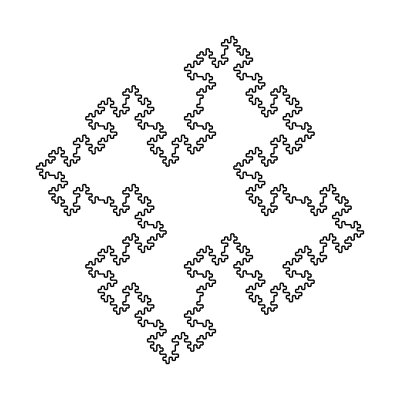

```mathematica
Graphics[ParseDirective[dir]]
```

#### Example 1.2 : Islands and lakes

```mathematica
ω=StringToDirective["F+F+F+F"];
rule={
"Forward"[]->Sequence@@StringToDirective["F+f-FF+F+FF+Ff+FF-f+FF-F-FF-Ff-FFF"],
"forward"[]->Sequence@@StringToDirective["ffffff"]
};
```

```mathematica
dir=Nest[ReplaceAll[rule],ω,2];
```

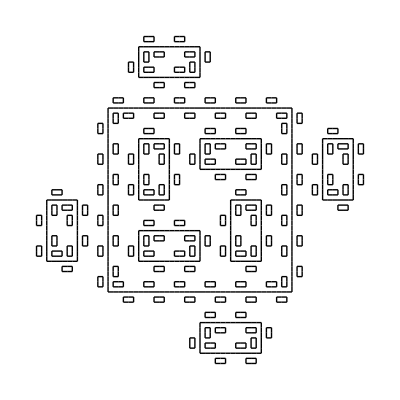

```mathematica
Graphics[ParseDirective[dir]]
```

#### Example 1.3: Sierpiński gasket

```mathematica
ω=StringToDirective["F(r)"];
rule={
"Forward"[l]->Sequence@@StringToDirective["F(r)+F(l)+F(r)"],
"Forward"[r]->Sequence@@StringToDirective["F(l)-F(r)-F(l)"]
};
normalizationRules={
"Forward"[l|r]:>"Forward"[]
};
```

```mathematica
dir=Nest[ReplaceAll[rule],ω,6]/.normalizationRules;
```

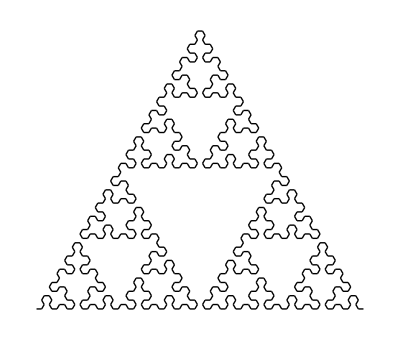

```mathematica
Graphics[ParseDirective[dir,"Left"->{π/3},"Right"->{π/3}]]
```

### 2

#### Example 2.1: Bracketed OL-system

```mathematica
ω=StringToDirective["X"];
rule={
"X"[]->Sequence@@StringToDirective["F-[[X]+X]+F[+FX]-X"],
"Forward"[]->Sequence@@StringToDirective["FF"]
};
```

```mathematica
dir=Nest[ReplaceAll[rule],ω,5];
```

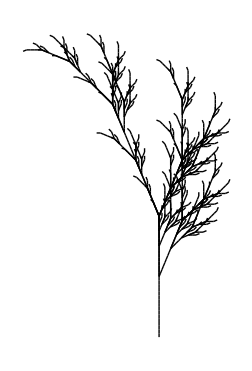

```mathematica
Graphics[
ParseDirective[
dir,
InitialState->{{0,0},90°},
"Left"->{22.5°},"Right"->{22.5°}
]
]
```

#### Example 2.2 : Binary tree

```mathematica
ω=StringToDirective["A"];
rule={
"A"[]->Sequence@@StringToDirective["F(1)[+A][A][-A]"],
"Forward"[s_]:>Evaluate[Sequence@@StringToDirective["F(s*R)"]]
};
paramRules={R->2};
```

```mathematica
dir=Nest[ReplaceAll[rule],ω,8]/.paramRules;
```

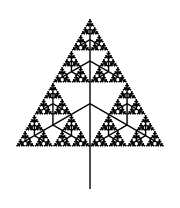

```mathematica
Graphics[
ParseDirective[
dir,
InitialState->{{0,0},90°},
"Left"->{120°},"Right"->{120°}
]
]
```

```mathematica
ω=StringToDirective["A"];
rule={
"A"[]->Sequence@@StringToDirective["F(1)[+++A][+A][-A][---A]"],
"Forward"[s_]:>Evaluate[Sequence@@StringToDirective["F(s*R)"]]
};
paramRules={R->(2)^(5/4)};
```

```mathematica
dir=Nest[ReplaceAll[rule],ω,7]/.paramRules;
```

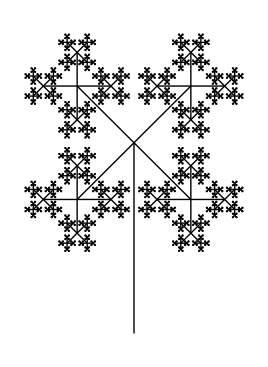

```mathematica
Graphics[
ParseDirective[
dir,
InitialState->{{0,0},90°},
"Left"->{45°},"Right"->{45°}
]
]
```

```mathematica
ParseDirective[{"Forward"[],"Bend"[]}]
```

{Line[{{0,0},{1,0}}],Circle[{1,1},1,{π/2,π}]}

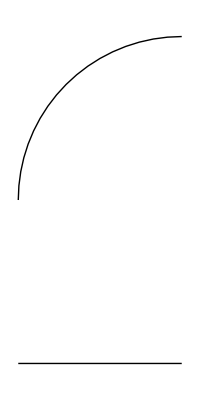

```mathematica
Graphics[ParseDirective[{"Forward"[],"Bend"[]}]]
```